```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
(* cf: A073058*)
(* F. M. Dekking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.15*)
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]]; 
m=Transpose[CompanionMatrix[(-1-x^2+x^3)*(x^2+x+1),x] ]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{1,1,2,0,0}}

```mathematica
(* 5 symbol substitution  for second cubic as  product pentic:1+x+2 x^2-x^5*)
```

```mathematica
n0=5
```

5

```mathematica
(* substitution *)
```

```mathematica
s[1]={2,0,0,0,0,0,0,0}; s[2]={3,0,0,0,0,0,0,0}; s[3]={4,0,0,0,0,0,0,0}; s[4]={5,0,0,0,0,0,0,0,0};s[5]={1,2,3,3,0,0,0,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{1,1,2,0,0}}

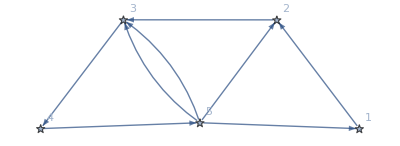

```mathematica
AdjacencyGraph[M,VertexLabels->"Name",ImageSize->Full,VertexShapeFunction->"Star"]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

1+x+2 x^2-x^5

```mathematica
z=x/.NSolve[CharacteristicPolynomial[M,x]==0,x][[3]]
```

-0.232786-0.792552 ⅈ

```mathematica
Abs[%]
```

0.826031

```mathematica
Clear[s,p]
```

```mathematica
(* program to express the substitution *)
```

```mathematica
Clear[s,t,p]
```

```mathematica
s[1]={2}; s[2]={3}; s[3]={4}; s[4]={5};s[5]={1,2,3,3};
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Flatten[Table[s[i],{i,5}]]
```

{2,3,4,5,1,2,3,3}

```mathematica
p[0]={1};p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[38];
```

```mathematica
Length[aa]
```

808627

```mathematica
(* graphing subroutine*)
```

```mathematica
x/.NSolve[CharacteristicPolynomial[M,x]==0,x][[3]]
```

-0.232786-0.792552 ⅈ

```mathematica
v=Table[N[{Re[z^i],Im[z^i]}],{i,5}]
```

{{-0.232786,-0.792552},{-0.57395,0.368989},{0.42605,0.368989},{0.193265,-0.423563},{-0.380685,-0.0545732}}

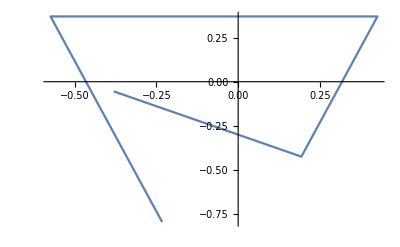

```mathematica
ListLinePlot[v]
```

```mathematica
bb=aa/. 1->v[[1]]/. 2->v[[2]]/. 3->v[[3]]/. 4->v[[4]]/. 5->v[[5]];
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g0=Rasterize[ListPlot[cc,PlotRange->All,Axes->False,ImageSize->{2000,2000},PlotStyle->{PointSize[0.001]},ColorFunction->Hue],RasterSize->2000,ImageSize->2000]
```

$Failed

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue" ,"Cyan","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
dd=Flatten[ParallelTable[{PointSize[0.001],cols[[aa[[n]]]],Point[cc[[n]]]},{n,Min[Length[cc],Length[aa]]}]];
```

```mathematica
g1=Rasterize[Show[Graphics[dd],ImageSize->{2000,2000},Background->Black],RasterSize->2000,ImageSize->2000]
```

$Failed

```mathematica
Export["5Symbol_2nd_cubic_rootpowers_level38_1.jpg",g0]
```

$Failed

```mathematica
Export["5Symbol_2nd_cubic_rootpowers_level38_2.jpg",g1]
```

$Aborted

```mathematica
(*end*)
```